```mathematica
bridgeless[graph_]:=(¬MemberQ[Total[GraphDistanceMatrix[graph]],1])
```

```mathematica
gt3d[graph_]:=((¬MemberQ[VertexDegree[graph],1])∧(¬MemberQ[VertexDegree[graph],2]))
```

```mathematica
GraphData[3;4]
```

{{4,2},{4,3},{4,6},ClawGraph,DiamondGraph,{Empty,4},{LadderRung,2},{Path,4},PawGraph,SquareGraph,TetrahedralGraph}

```mathematica
Select[GraphData[3;10],ConnectedGraphQ[GraphData[#]]∧SimpleGraphQ[GraphData[#]]∧gt3d[GraphData[#]]∧bridgeless[GraphData[#]]&]
```

{{Antiprism,5},{Barbell,5},{BlackBishop,{4,5}},{Circulant,{10,{1,4}}},{Circulant,{10,{1,2,3}}},{Circulant,{10,{1,2,4}}},{Circulant,{10,{1,2,5}}},{Circulant,{10,{1,4,5}}},{Circulant,{10,{2,4,5}}},{Circulant,{10,{1,2,4,5}}},{CocktailParty,5},{Complete,10},{CompleteBipartite,{3,7}},{CompleteBipartite,{4,6}},{CompleteBipartite,{5,5}},{CompleteTripartite,{1,4,5}},{CompleteTripartite,{2,3,5}},{CompleteTripartite,{2,4,4}},{CompleteTripartite,{3,3,4}},{Cone,{3,7}},{Cone,{4,6}},{Cone,{5,5}},{Cone,{6,4}},{Cone,{7,3}},{Crown,5},{Cubic,{10,1}},{Cubic,{10,2}},{Cubic,{10,3}},{Cubic,{10,4}},{Cubic,{10,5}},{Cubic,{10,6}},{Cubic,{10,7}},{Cubic,{10,8}},{Cubic,{10,9}},{Cubic,{10,10}},{Cubic,{10,11}},{Cubic,{10,12}},{Cubic,{10,13}},{Cubic,{10,14}},{Cubic,{10,16}},{Cubic,{10,18}},{Fan,{2,8}},{Fan,{3,7}},{Fan,{4,6}},{Fan,{5,5}},GolombGraph,{JohnsonSkeleton,15},{JohnsonSkeleton,17},{JohnsonSkeleton,62},{JohnsonSkeleton,64},{JohnsonSkeleton,86},{King,{2,5}},{MoebiusLadder,5},PetersenGraph,{Prism,5},{Quartic,{10,1}},{Quartic,{10,2}},{Quartic,{10,3}},{Quartic,{10,4}},{Quartic,{10,5}},{Quartic,{10,6}},{Quartic,{10,7}},{Quartic,{10,8}},{Quartic,{10,9}},{Quartic,{10,10}},{Quartic,{10,11}},{Quartic,{10,12}},{Quartic,{10,13}},{Quartic,{10,14}},{Quartic,{10,15}},{Quartic,{10,16}},{Quartic,{10,18}},{Quartic,{10,20}},{Quartic,{10,21}},{Quartic,{10,22}},{Quartic,{10,23}},{Quartic,{10,24}},{Quartic,{10,25}},{Quartic,{10,26}},{Quartic,{10,27}},{Quartic,{10,28}},{Quartic,{10,29}},{Quartic,{10,30}},{Quartic,{10,31}},{Quartic,{10,32}},{Quartic,{10,33}},{Quartic,{10,34}},{Quartic,{10,35}},{Quartic,{10,36}},{Quartic,{10,37}},{Quartic,{10,38}},{Quartic,{10,39}},{Quartic,{10,40}},{Quartic,{10,41}},{Quartic,{10,42}},{Quartic,{10,43}},{Quartic,{10,44}},{Quartic,{10,45}},{Quartic,{10,46}},{Quartic,{10,47}},{Quartic,{10,48}},{Quartic,{10,49}},{Quartic,{10,50}},{Quartic,{10,51}},{Quartic,{10,52}},{Quartic,{10,53}},{Quartic,{10,54}},{Quartic,{10,55}},{Quartic,{10,56}},{Quartic,{10,57}},{Queen,{2,5}},{Quintic,{10,1}},{Quintic,{10,2}},{Quintic,{10,4}},{Quintic,{10,5}},{Quintic,{10,6}},{Quintic,{10,7}},{Quintic,{10,8}},{Quintic,{10,9}},{Quintic,{10,10}},{Quintic,{10,11}},{Quintic,{10,12}},{Quintic,{10,14}},{Quintic,{10,15}},{Quintic,{10,16}},{Quintic,{10,17}},{Quintic,{10,18}},{Quintic,{10,19}},{Quintic,{10,20}},{Quintic,{10,21}},{Quintic,{10,22}},{Quintic,{10,23}},{Quintic,{10,24}},{Quintic,{10,25}},{Quintic,{10,26}},{Quintic,{10,27}},{Quintic,{10,28}},{Quintic,{10,29}},{Quintic,{10,30}},{Quintic,{10,31}},{Quintic,{10,32}},{Quintic,{10,33}},{Quintic,{10,34}},{Quintic,{10,35}},{Quintic,{10,36}},{Quintic,{10,37}},{Quintic,{10,38}},{Quintic,{10,39}},{Quintic,{10,40}},{Quintic,{10,41}},{Quintic,{10,42}},{Quintic,{10,43}},{Quintic,{10,44}},{Quintic,{10,45}},{Quintic,{10,46}},{Quintic,{10,47}},{Quintic,{10,48}},{Quintic,{10,49}},{Quintic,{10,50}},{Quintic,{10,51}},{Quintic,{10,52}},{Quintic,{10,53}},{Quintic,{10,54}},{Quintic,{10,55}},{Quintic,{10,56}},{Quintic,{10,57}},{Quintic,{10,58}},{Septic,{10,1}},{Septic,{10,2}},{Septic,{10,4}},{Sextic,{10,1}},{Sextic,{10,2}},{Sextic,{10,3}},{Sextic,{10,4}},{Sextic,{10,5}},{Sextic,{10,6}},{Sextic,{10,9}},{Sextic,{10,10}},{Sextic,{10,11}},{Sextic,{10,12}},{Sextic,{10,13}},{Sextic,{10,14}},{Sextic,{10,15}},{Sextic,{10,16}},{Sextic,{10,17}},{Sextic,{10,21}},{TorusGrid,{4,6}},{TorusGrid,{5,5}},{Triangular,5},{TriangularHoneycombQueen,4},{Turan,{10,4}},{Turan,{10,6}},{Turan,{10,7}},{Turan,{10,8}},{Turan,{10,9}},{Wheel,10},{Windmill,{3,4}}}

```mathematica
Select[Out[158],gord[GraphData[#]]==1&]
```

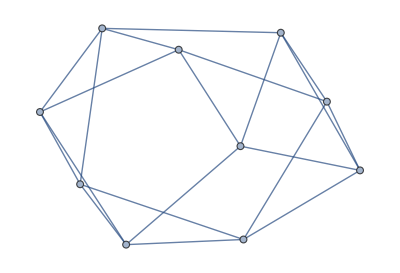
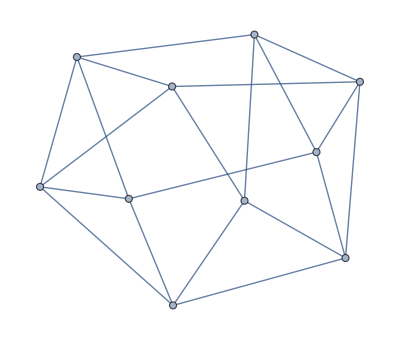
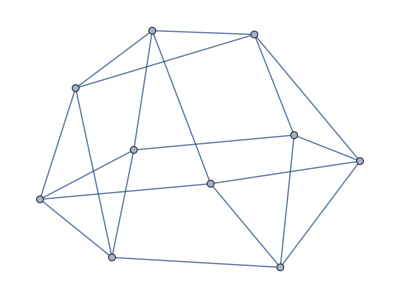
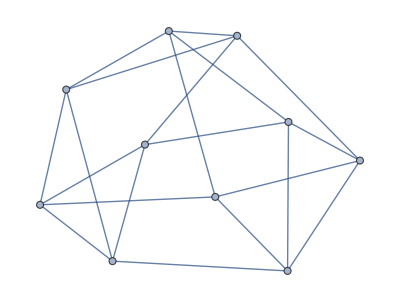
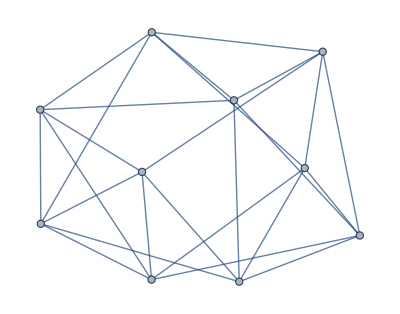
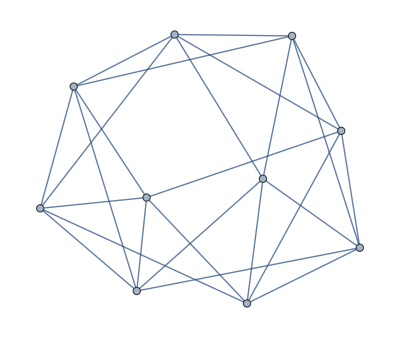
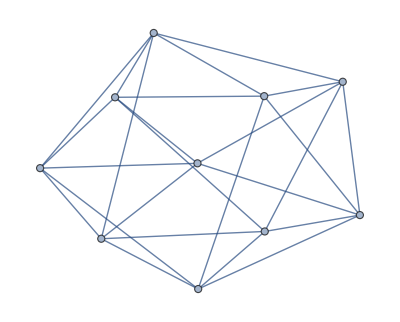
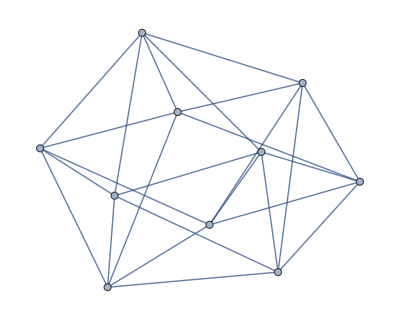

```mathematica
Map[GraphData,{{"Quartic",{10,22}},{"Quartic",{10,30}},{"Quartic",{10,31}},{"Quartic",{10,39}},{"Quintic",{10,25}},{"Quintic",{10,26}},{"Quintic",{10,37}},{"Quintic",{10,39}}}]
```

```mathematica
Map[Length[EdgeList[#]]&,%]
```

{20,20,20,20,25,25,25,25}

```mathematica
EdgeList[-Graphics-]
```

```mathematica
Map[{#[[1]],#[[2]]}&,{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->6,3<->5,3<->7,4<->6,4<->8,5<->8,5<->9,6<->9,6<->10,7<->8,7<->9,7<->10,8<->10,9<->10}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,6},{3,5},{3,7},{4,6},{4,8},{5,8},{5,9},{6,9},{6,10},{7,8},{7,9},{7,10},{8,10},{9,10}}

```mathematica
h2[n_]:=Block[{blist=PadLeft[IntegerDigits[n,2],20],uelist={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,6},{3,5},{3,7},{4,6},{4,8},{5,8},{5,9},{6,9},{6,10},{7,8},{7,9},{7,10},{8,10},{9,10}}},
Length[FindCycle[Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,20}]],∞,All]]]
```

```mathematica
Monitor[First[Last[Reap[Do[If[h2[j]>50,Sow[j]],{j,0,2^20}]]]],{j,i}]
```

{86923,100509,100622,100749,100758,101134,101262,102790,102795,103302,103307,103310,103311,104718,104838,104843,104845,104846,104847,104854,105230,105350,105355,105358,105359,119691,140393,140400,140401,140402,140404,140409,140529,140905,140912,140913,140914,141041,141162,142452,142457,144745,145121,145250,157289,157298,157425,157538,157546,206065,206176,206178,206180,206185,206194,206577,210274,210290,210401,214854,217739,217995,222945,222961,223074,223082,232077,232086,232206,232334,232335,234254,234374,234378,234379,234381,234382,234383,234410,236302,236422,236427,236430,236431,250507,250763,251787,301205,301206,301213,301326,301342,301453,301462,301718,301838,301966,318222,329885,330014,330134,332683,334094,334221,334230,334606,334734,346398,346765,346774,346779,346781,346782,346783,346894,346910,349062,349066,349067,349069,349070,349071,349098,350478,350614,350990,351110,351115,351118,351119,362637,362644,362645,362646,362649,362651,362652,362653,362654,362655,362684,362685,362764,362765,362766,362774,362778,362782,362783,362893,362902,362909,362910,363158,363165,363166,363167,363278,363294,363414,363422,363677,363709,364933,364934,364939,364941,364942,364943,364947,364950,364951,365446,365451,365454,365455,366001,366725,366733,366739,366740,366741,366742,366743,366745,366747,366749,366751,366772,366777,366805,366807,366854,366858,366859,366860,366861,366862,366863,366874,366878,366927,366980,366981,366982,366985,366987,366988,366989,366990,366991,366994,366995,366997,366998,366999,367002,367003,367005,367006,367007,367020,367034,367053,367059,367062,367063,367254,367255,367371,367374,367375,367494,367499,367500,367501,367502,367503,367510,367511,367514,367515,367518,367765,367793,367797,367801,367829,368021,368049,368053,368057,368085,374933,375054,375181,375190,379037,379166,379533,379542,379547,379549,379550,379551,379662,379678,380061,381830,381835,381838,381839,383125,383246,383366,383371,383373,383374,383375,383382,383638,383639,383755,383758,383759,383878,383883,383885,383886,383887,383894,384149,384270,384397,384406,404592,404596,404601,412174,418929,419057,419433,419442,419569,419690,420980,430987,432398,432781,432790,432907,432910,432911,433038,433039,433337,463755,493854,494230,496518,496523,497813,497934,498061,498062,498063,498070,498446,498566,498571,498573,498574,498575,498582,549993,550000,550001,550002,550004,550009,550129,550505,550512,550513,550514,550641,550762,552052,552057,554345,554721,584820,615238,615536,615537,615664,615665,615668,615785,615794,616177,617588,627595,628885,629006,629133,629142,629518,629646,636401,643974,643979,643983,664169,664178,664305,664426,664681,664688,664689,664690,664692,664697,664816,664817,664820,664936,664937,665193,665200,665201,665202,665204,665209,665329,665450,666736,666737,666740,666745,668514,668897,668913,669024,669025,669026,669028,669033,669042,669409,669538,673385,673394,673521,673642,680490,680518,680522,680526,680554,680746,680774,680778,680782,680810,681057,681060,681061,681064,681065,681072,681073,681074,681075,681076,681081,681200,681201,681204,681320,681321,681512,681513,681516,681522,681541,681555,681568,681569,681570,681572,681573,681576,681577,681578,681580,681581,681584,681585,681586,681587,681588,681590,681593,681594,681595,681648,681697,681701,681712,681713,681714,681715,681716,681717,681721,681768,681770,681798,681803,681824,681826,681828,681830,681832,681833,681834,681835,681836,681842,681850,682574,683120,683121,683124,683129,683624,683625,683628,683632,683633,683634,683636,683641,683642,684866,684898,685153,685161,685281,685297,685408,685409,685410,685417,685665,685666,685673,685682,685792,685793,685797,685801,685809,685810,685811,685890,685891,685920,685921,685922,685923,685924,685926,685929,685930,685931,685938,697456,697457,697460,697465,697585,697961,698097,699477,699504,699505,699506,699508,699509,699513,701665,701681,701792,701793,701794,701796,701801,701810,702177,713841,713969,714345,714354,714481,715892,718441,718561,718690,730353,746609,746737,746857,747113,747122,747233,747249,747362,747369,747370,796788,797812,798068,812144,812145,812148,812153,812273,814165,814192,814193,814194,814196,814197,814201,814321,816240,816241,816369,816489,816498,825493,825501,825614,825630,830580,830836,833721,838174,838285,838301,841998,842381,842390,842395,842397,842399,842510,891029,891037,891150,891277,891286,903325,903454,903830,906118,906123,907413,907534,907661,907662,907663,907670,908046,908166,908171,908173,908174,908175,908182,928884,943216,943217,943220,943225,943345,943721,943728,943729,943730,943732,943737,943857,945264,945265,945268,945273,945780,945785,947313,947441,947817,947826,947953,948066,961652}

```mathematica
Max[Table[h2[RandomInteger[{0,2^20}]],{i,1,1000}]]
```

50

```mathematica
Map[gt3d[GraphData[#]]&,%150]
```

```mathematica
gord[graph_]:=GroupOrder[GraphAutomorphismGroup[graph]]
```

```mathematica
Total[GraphDistanceMatrix[CompleteGraph[4]]]
```

{3,3,3,3}

```mathematica
halfable[graph_]:=
If[EvenQ[Length[VertexList[graph]]],Total[Map[Boole[IsomorphicGraphQ[Subgraph[graph,#],Subgraph[graph,Complement[VertexList[graph],#]]]]&,Subsets[VertexList[graph],{Length[VertexList[graph]]/2}]]],Sum[Total[Map[Boole[IsomorphicGraphQ[Subgraph[graph,#],Subgraph[graph,Complement[withoutn[VertexList[graph],i],#]]]]&,Subsets[withoutn[VertexList[graph],i],{(Length[VertexList[graph]]-1)/2}]]],{i,1,Length[VertexList[graph]]}]]
```

```mathematica
withoutn[list_,n_]:=Complement[list,{n}]
```

```mathematica
Map[halfable,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{68,72,64,78,72,78,68,64}

```mathematica
Out[158][[1]]
```

{Antiprism,5}

```mathematica
GraphData[Out[158][[40]]]
```

```mathematica
Length[Out[158]]
Monitor[Table[halfable[GraphData[Out[158][[j]]]],{j,1,197}],{j,i}]
```

197

{152,140,24,232,152,152,152,232,252,152,252,252,0,120,252,10,20,140,120,0,120,0,120,0,252,88,80,84,96,84,84,104,96,104,48,102,84,88,144,136,120,64,0,72,20,6,124,108,40,36,64,80,152,72,152,120,124,88,84,66,58,48,120,88,44,84,56,42,84,96,68,76,76,108,68,60,88,64,64,58,72,88,72,64,62,54,96,72,86,96,80,78,108,74,96,92,60,68,88,84,62,96,140,68,48,108,82,62,112,116,72,96,84,96,116,72,42,48,58,60,66,96,112,108,120,68,48,72,82,68,64,54,62,72,78,44,88,140,96,86,88,96,124,88,74,68,88,64,56,84,88,64,80,84,68,58,76,62,76,84,120,108,92,108,60,62,124,168,120,84,120,84,144,96,88,102,104,136,88,84,120,104,84,96,80,84,120,152,72,48,120,140,120,120,140,0,0}

```mathematica
Flatten[Position[%,0]]
```

```mathematica
197 is 1-v-con
```

```mathematica
halfable[GraphData["FruchtGraph"]]
```

222

```mathematica
EdgeList[GraphData["FruchtGraph"]]
Map[{#[[1]],#[[2]]}&,%]

h3[n_]:=Block[{blist=PadLeft[IntegerDigits[n,2],18],uelist={{1,2},{1,7},{1,11},{2,3},{2,8},{3,4},{3,9},{4,5},{4,9},{5,6},{5,10},{6,7},{6,10},{7,11},{8,11},{8,12},{9,12},{10,12}}},
Length[FindCycle[Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,18}]],∞,All]]]
```

{1<->2,1<->7,1<->11,2<->3,2<->8,3<->4,3<->9,4<->5,4<->9,5<->6,5<->10,6<->7,6<->10,7<->11,8<->11,8<->12,9<->12,10<->12}

{{1,2},{1,7},{1,11},{2,3},{2,8},{3,4},{3,9},{4,5},{4,9},{5,6},{5,10},{6,7},{6,10},{7,11},{8,11},{8,12},{9,12},{10,12}}

```mathematica
Monitor[Table[(Length[FindCycle[Block[{blist=PadLeft[IntegerDigits[n,2],18],uelist={{1,2},{1,7},{1,11},{2,3},{2,8},{3,4},{3,9},{4,5},{4,9},{5,6},{5,10},{6,7},{6,10},{7,11},{8,11},{8,12},{9,12},{10,12}}},
Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,18}]]],∞,All]]≥18),{n,1,2^18}],n]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,262038,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}
 |  |  |  |

```mathematica
Flatten[Position[Out[1],True]]
```

```mathematica
Map[Block[{blist=PadLeft[IntegerDigits[#,2],18],uelist={{1,2},{1,7},{1,11},{2,3},{2,8},{3,4},{3,9},{4,5},{4,9},{5,6},{5,10},{6,7},{6,10},{7,11},{8,11},{8,12},{9,12},{10,12}}},
Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,18}]]]&,{73897,74283,100906,100907,161236,161237,187860,188246}]
```

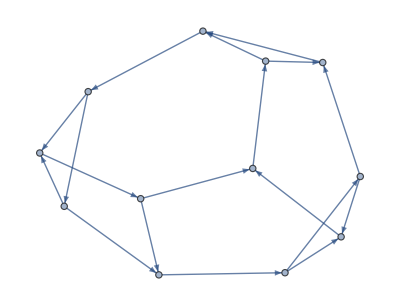
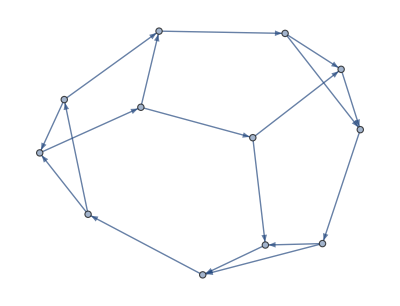
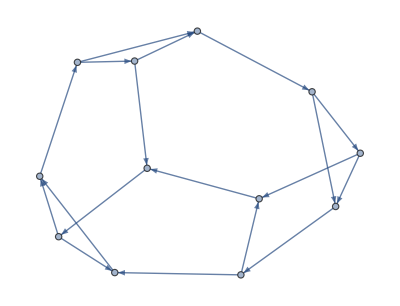
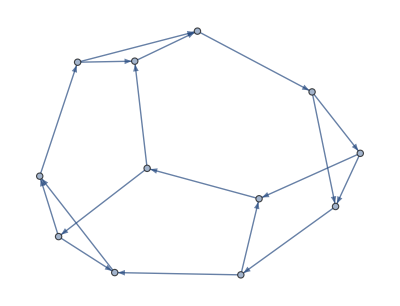
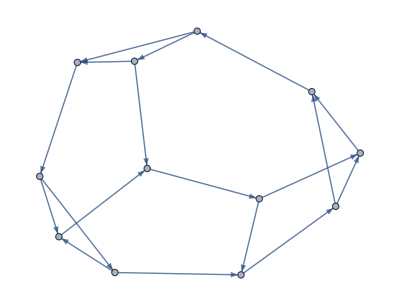
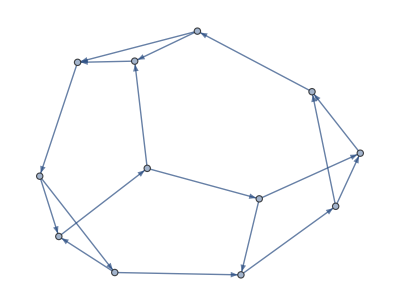
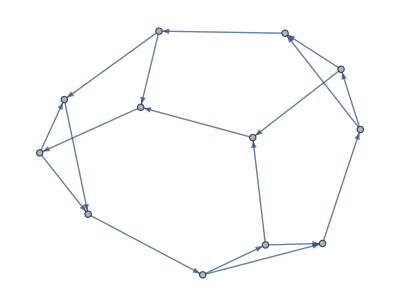
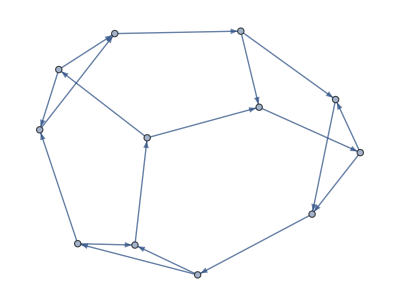
```mathematica
Map[Length[FindCycle[#,∞,All]]&,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{19,18,18,19,19,18,18,19}

```mathematica
Monitor[Table[h3[n],{n,0,2^18}],n]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,261821,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

```mathematica
Max[%]
```

19

```mathematica
Flatten[Position[Out[256],19]]
```

{73898,100908,161237,188247}

```mathematica
Block[{blist=PadLeft[IntegerDigits[161237,2],18],uelist={{1,2},{1,7},{1,11},{2,3},{2,8},{3,4},{3,9},{4,5},{4,9},{5,6},{5,10},{6,7},{6,10},{7,11},{8,11},{8,12},{9,12},{10,12}}},
Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,18}]]]
```

-Graphics-

```mathematica
Length[FindCycle[-Graphics-,∞,All]]
```

18

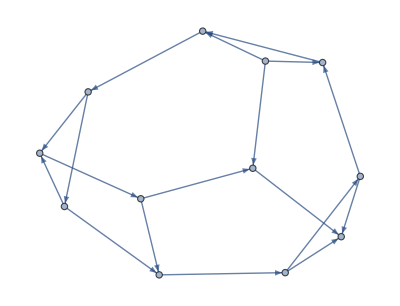
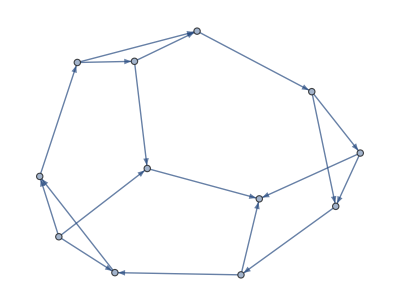
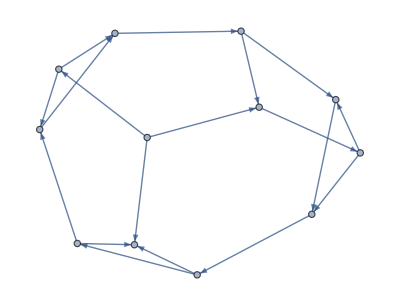
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Block[{blist=PadLeft[IntegerDigits[#,2],18],uelist={{1,2},{1,7},{1,11},{2,3},{2,8},{3,4},{3,9},{4,5},{4,9},{5,6},{5,10},{6,7},{6,10},{7,11},{8,11},{8,12},{9,12},{10,12}}},
Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,18}]]]&,Flatten[Position[Out[256],19]]]
```

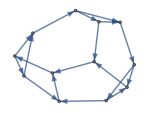
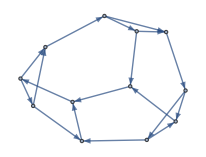
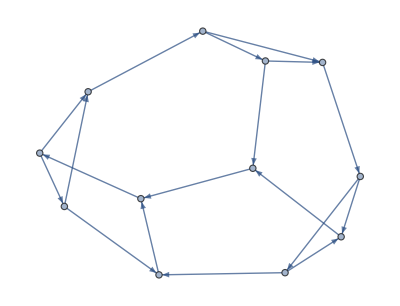
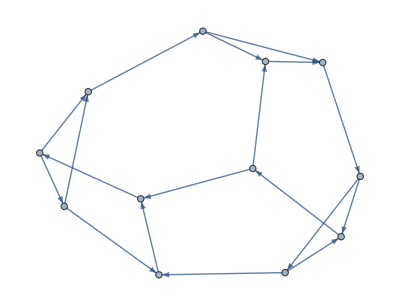
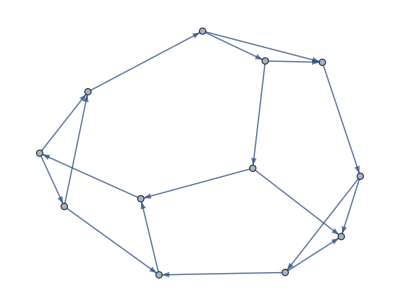
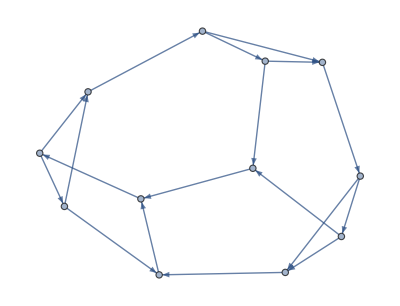
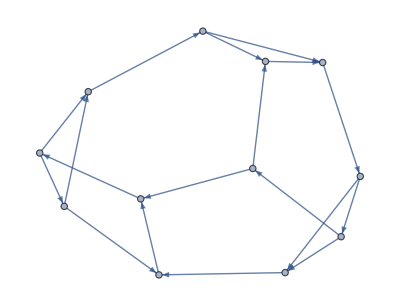
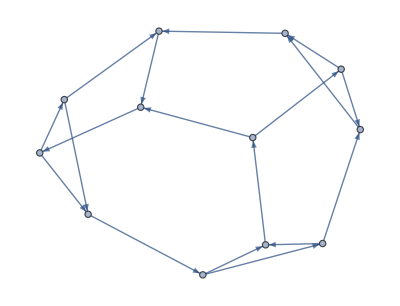
```mathematica
Map[signedplot,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

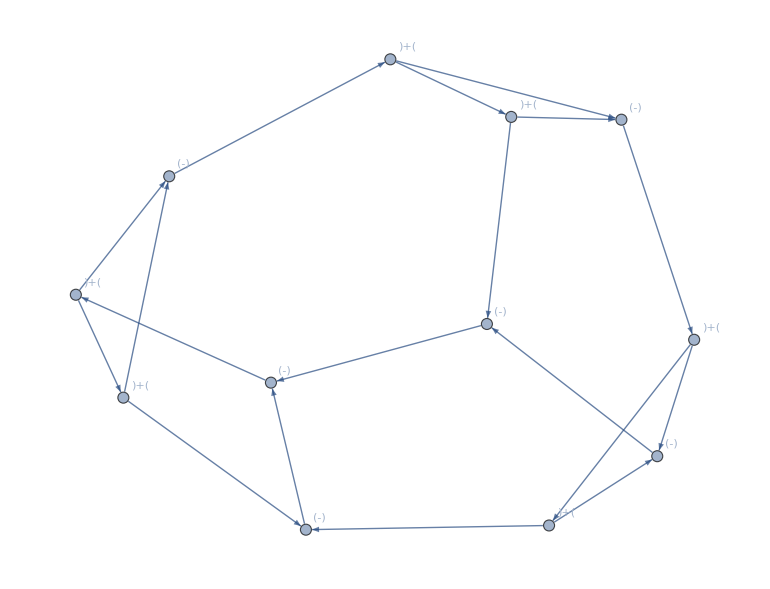
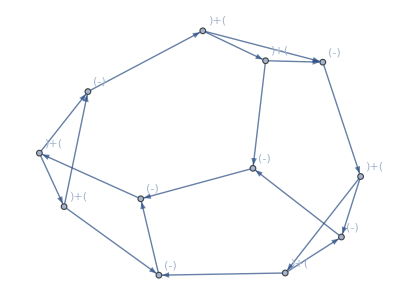
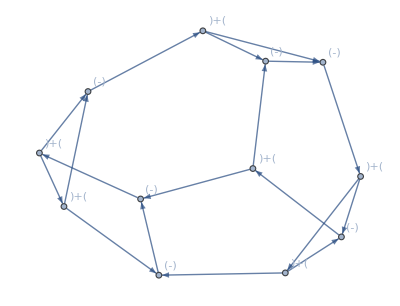
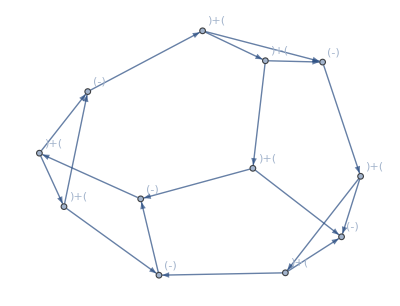
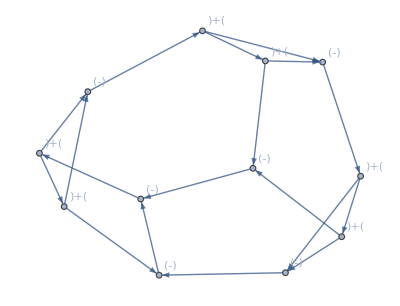
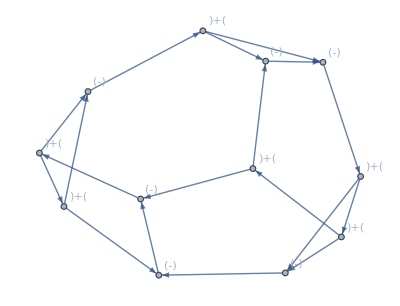
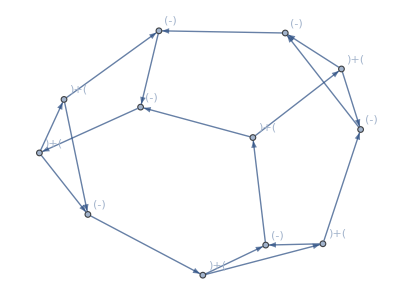
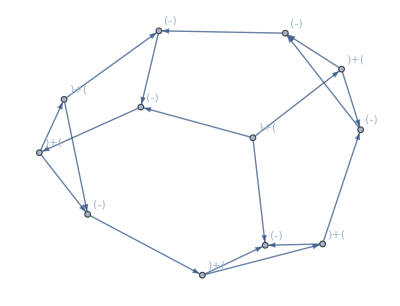
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[{{1,2},{1,7},{1,11},{2,3},{2,8},{3,4},{3,9},{4,5},{4,9},{5,6},{5,10},{6,7},{6,10},{7,11},{8,11},{8,12},{9,12},{10,12}}]
```

18

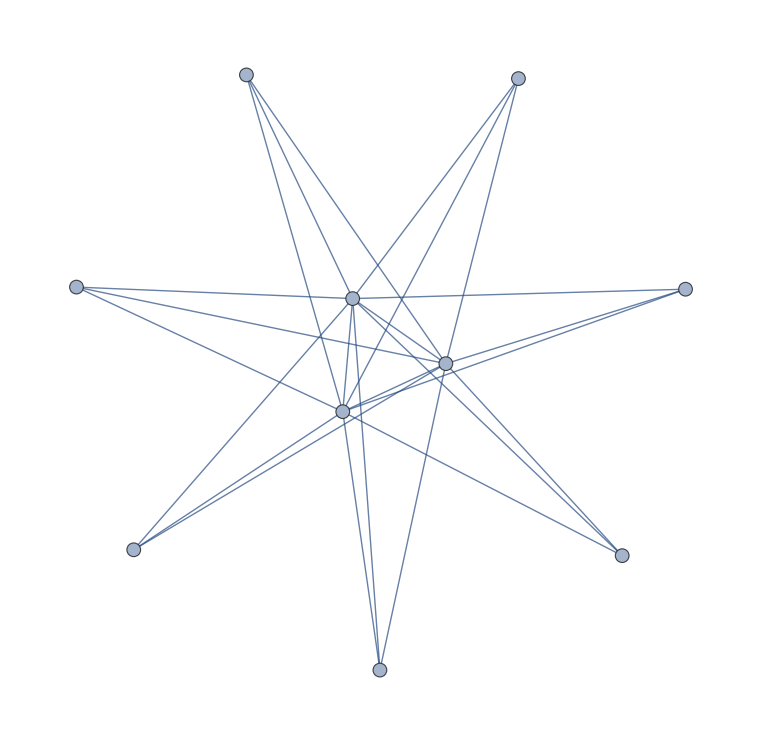

```mathematica
GraphData[{"Cone",{3,7}}]
```

```mathematica
Map[Out[158][[#]]&,{13,20,22,24,43,196}]
```

{{CompleteBipartite,{3,7}},{Cone,{3,7}},{Cone,{5,5}},{Cone,{7,3}},{Fan,{3,7}},{Wheel,10}}

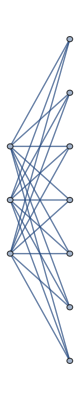
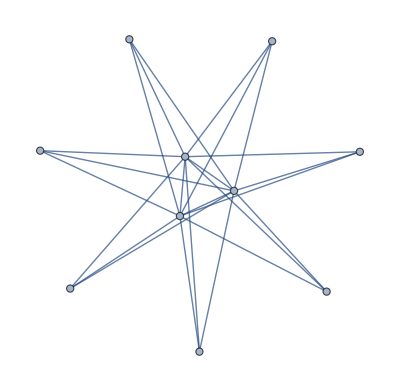
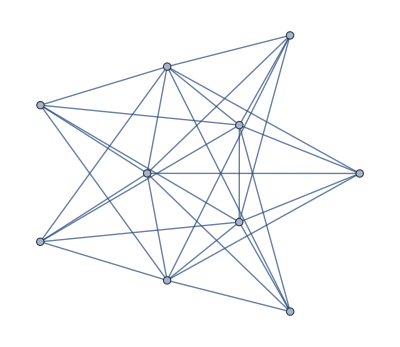
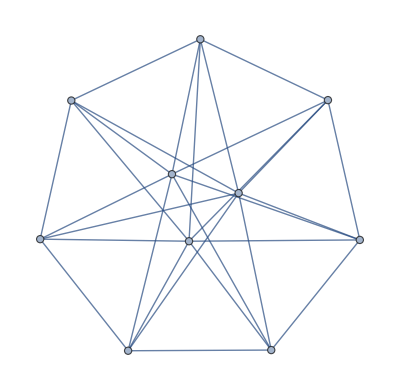
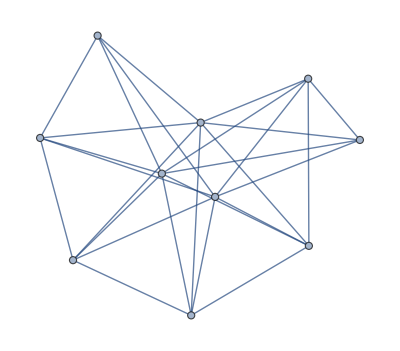
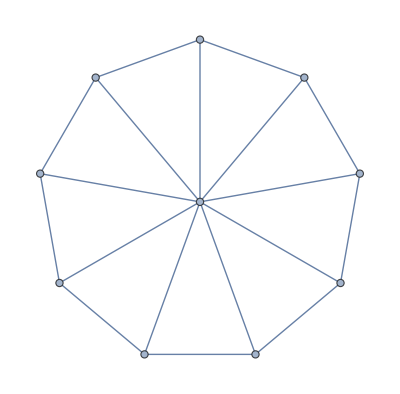

```mathematica
Map[GraphData[Out[158][[#]]]&,{13,20,22,24,43,196}]
```

```mathematica
"∃G:(∃2 e-paths b/n any pair) ∧ (∃2 v-paths b/n any pair) ∧ ¬(∃d_i==2) ∧ ¬(∃ halfing of G) ?????"
```

```mathematica
trim[graph_]:=Subgraph[graph,Select[VertexList[graph],VertexDegree[graph,#]>1&]]
```

```mathematica
collapseaux[pair_,vcycle0_,vn0_]:=Piecewise[{{{vn0,pair[[2]]}, MemberQ[vcycle0,pair[[1]]]}, {{pair[[1]],vn0}, MemberQ[vcycle0,pair[[2]]]}}]
collapse[graph_,vcycle_]:=(*delete edges connecting vcycle and collapse to single vertex*)Block[{vn=Length[VertexList[graph]]+1,list1=
Block[{pairs=Subsets[vcycle,{2}]},Select[Map[{#[[1]],#[[2]]}&,EdgeList[graph]],¬IntersectingQ[pairs,#]&]]},

trim[Graph[DeleteDuplicates[Map[#[[1]]->#[[2]]&,Join[Select[list1,¬IntersectingQ[vcycle,#]&],
Map[collapseaux[#,vcycle,vn]&,Select[list1,IntersectingQ[vcycle,#]&]]]]]]]]
```

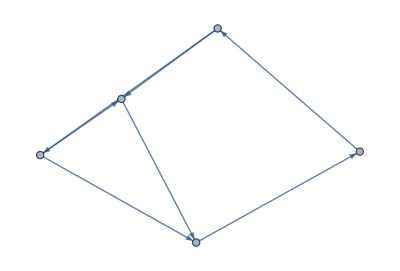

3

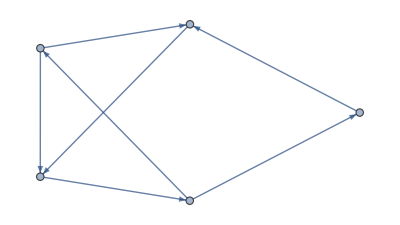
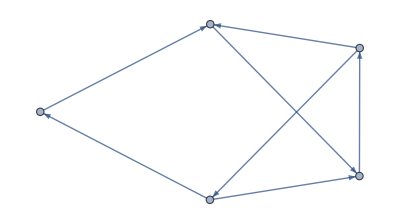
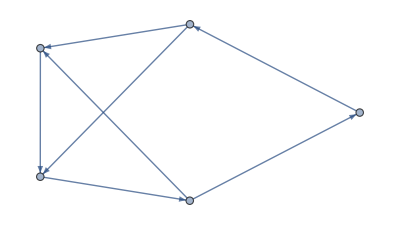
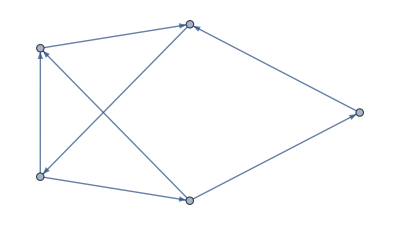
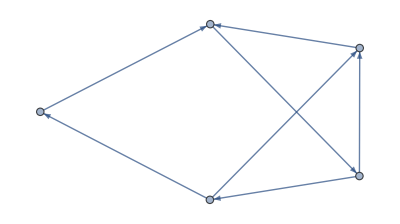
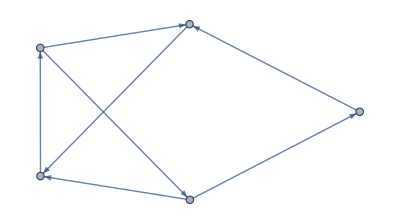
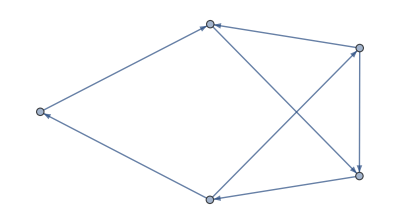
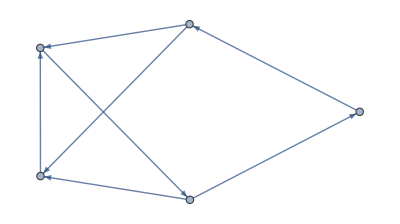
{{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3},{-Graphics-,3}}

```mathematica
cled=collapse[-Graphics-,DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,FindCycle[-Graphics-,∞,All][[6]]]]]]
Length[FindCycle[cled,∞,All]]
Map[{#,Length[FindCycle[#,∞,All]]}&,maxorientations[UndirectedGraph[cled]]]
```

```mathematica
Length[FindCycle[Out[22],∞,All]]
```

3

```mathematica
posmax[list_]:=Block[{max=Max[list]},Flatten[Position[list,max]]]
```

```mathematica
maxorientations[graph_]:=Block[{len=Length[EdgeList[graph]]},Map[Block[{blist=PadLeft[IntegerDigits[#,2],len],uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]]},Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]]]&,
posmax[
Table[Block[{blist=PadLeft[IntegerDigits[n,2],len],uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]]},
Length[FindCycle[Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]],∞,All]]],{n,1,2^len}]]]]
```

```mathematica
maxorientations2[graph_]:=Monitor[Block[{j=0,blist={},bestlist={},bestlen=1,uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]],len=Length[EdgeList[graph]]},
For[j=0,j<2^len,j++,blist=PadLeft[IntegerDigits[j,2],len];
Block[{thislen=Length[FindCycle[Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]],∞,All]]},If[thislen≥bestlen,AppendTo[bestlist,{thislen,j}];bestlen=thislen]]];
Block[{allmax=Max[Map[First,bestlist]]},
Map[Graph[Table[Piecewise[{{Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[1]]->Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[2]], PadLeft[IntegerDigits[#,2],len][[i]]==0}, {Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[2]]->Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[1]], PadLeft[IntegerDigits[#,2],len][[i]]==1}}],{i,1,len}]]&,Map[Last,Select[bestlist,First[#]==allmax&]]]
]],{j,i}]
```

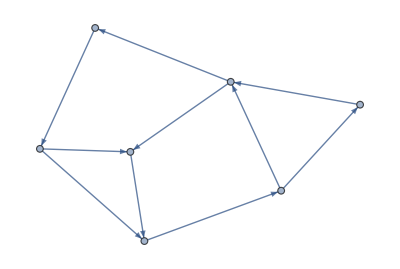
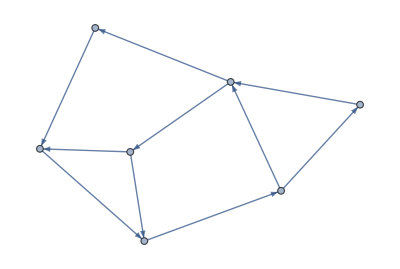
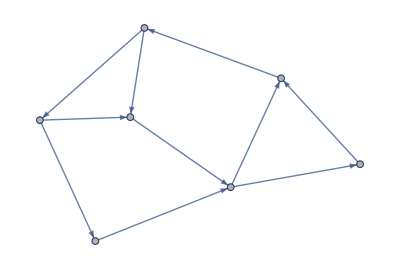
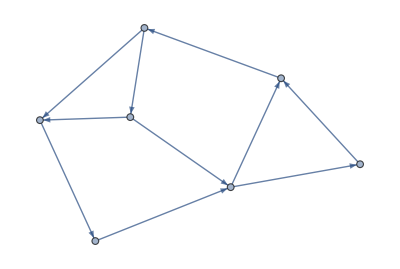

```mathematica
maxorientations2[UndirectedGraph[-Graphics-]]
```

```mathematica
Map[IsomorphicGraphQ[-Graphics-,#]&,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{False,False,False,False}